### Данные об ОДУ и методах

```mathematica
systems={
<|
"system"->{x'[t]==2 x[t]+y[t]^2-1,y'[t]==6 x[t]-y[t]^2+1},
"vars"->{x,y},
"id"->0
|>,
<|
"system"->{x'[t]==1-x[t]^2-y[t]^2,y'[t]==2x[t]},
"vars"->{x,y},
"id"->1
|>,
<|
"system"->{x'[t]==10(y[t]-x[t]),y'[t]==x[t](28-z[t])-y[t],z'[t]==x[t] y[t]-8/3 z[t]},
"vars"->{x,y,z},
"id"->2
|>,
<|
"system"->{Subscript[u, 1]'[t]==Subscript[u, 2][t],Subscript[u, 2]'[t]==-1/1 Subscript[u, 1][t]},
"vars"->{Subscript[u, 1],Subscript[u, 2]},
"id"->3
|>
};
```

```mathematica
methodIds=<|
"Рунге-Кутта 2-го порядка"->0,
"Рунге-Кутта 4-го порядка"->1,
"Явный метод Эйлера"->2,
"Неявный метод Эйлера"->3,
"Симметричная схема"->4,
"Адамса—Башфорта 4 порядка"->5,
"Метод предиктор–корректор 4 порядка"->6
|>;
```

### Взаимодействие с программой на C++

```mathematica
ChangeInputFile[fId_Integer,n_Integer,u0:{(_Integer|_Real)..},t0:(_Integer|_Real),T:(_Integer|_Real)]:=Module[{inputString,u0String},
u0String=StringRiffle@(ToString/@u0);
inputString=StringRiffle[ToString/@{fId,n,u0String,t0,T},"\n"];
Export["C:\\Users\\Alex\\Documents\\Qt\\BMSTU\\NumMethods Semester 6\\NumMethods_Sem6_Lab_1\\input.txt",inputString]
]
```

```mathematica
ChangeParametersFile[methodId_Integer,τ0:(_Integer|_Real),tol:(_Integer|_Real),ϵ:(_Integer|_Real),useStepReg_?BooleanQ]:=Module[{inputString},
inputString=StringRiffle[ToString/@{methodId,τ0,tol,ϵ,Boole@useStepReg},"\n"];
Export["C:\\Users\\Alex\\Documents\\Qt\\BMSTU\\NumMethods Semester 6\\NumMethods_Sem6_Lab_1\\parameters.txt",inputString]
]
```

```mathematica
RunCppApp[]:=Module[{rawData},
Run["cd C:\\Users\\Alex\\Documents\\Qt\\BMSTU\\NumMethods Semester 6\\NumMethods_Sem6_Lab_1\\release & NumMethods_Sem6_Lab_1.exe"];rawData=Import["C:\\Users\\Alex\\Documents\\Qt\\BMSTU\\NumMethods Semester 6\\NumMethods_Sem6_Lab_1\\output.txt","Table"];
<|
"all_t"->First /@rawData,
"all_y"->Rest/@rawData,
"all_t_with_first_y_comp"->Most/@rawData
|>
]
```

### Панель для тестирования

```mathematica
CreateTestPanel[]:=DynamicModule[{inputGrid,plotGrid,systemIndex=1,t0=0,T=1,initCoords={},methodName,τ0=0.1,tol=8,ϵ=0.01,wmPlot,numSolPlot,useStepReg,ShowGraphs,appRes=Null,initialValues,wmSolution,doOverlay=True},
initCoords=Table[0,Length@systems[[systemIndex,"vars"]]];
wmPlot=Style["\[WolframLanguageLogo]",50,Black];
numSolPlot=Style["C++",45,Black];

ShowGraphs[]:=DynamicModule[{overlayPlot},
If[appRes==Null,Return[]];

wmPlot=Switch[Length@systems[[systemIndex,"vars"]],
2,
ParametricPlot[Evaluate[(#[t]&)/@systems[[systemIndex,"vars"]]/.Evaluate@wmSolution],{t,t0,T},PlotStyle->Gray,AspectRatio->1],
3,
ParametricPlot3D[Evaluate[(#[t]&)/@systems[[systemIndex,"vars"]]/.Evaluate@wmSolution],{t,t0,T},PlotStyle->Gray,AspectRatio->1]
];

overlayPlot=If[doOverlay,wmPlot,Nothing];

numSolPlot=Switch[Length@systems[[systemIndex,"vars"]],
2,
Show@@{ListLinePlot[appRes[["all_y"]],AspectRatio->1,PlotStyle->{Thickness[0.012],Black}],overlayPlot},
3,
Show@@{ListLinePlot3D[appRes[["all_y"]],AspectRatio->1,PlotStyle->{Thick}],overlayPlot}
];
];

inputGrid=Grid[Transpose@{{
Text["Выбор примера:"],

SetterBar[Dynamic[systemIndex,{(systemIndex=#)&,(initCoords=PadRight[initCoords,Length@systems[[#,"vars"]]])&}],Range[Length@systems]],

Text["Система:"],

Dynamic[Grid[{
{Style["{",18*Length@systems[[systemIndex,"system"]],Black],First@systems[[systemIndex,"system"]]//TraditionalForm},
Sequence@@({SpanFromAbove,#}&/@(TraditionalForm/@Rest@systems[[systemIndex,"system"]]))
},
Alignment->{{Left,"=="},Center}
]],

Text["Отрезок интегрирования [t_0; T]:"],

Grid[{{
Text["t_0: "],
InputField[Dynamic[t0],Number,FieldSize->Tiny],
Text["\tT: "],
InputField[Dynamic[T],Number,FieldSize->Tiny]
}}],

Text["Начальная точка:"],

(*
Grid@Table[{
Text[With[{i=varInd},Dynamic[systems[[systemIndex,"vars",i]]]]],
InputField[With[{i=varInd},Dynamic[initCoords[[i]]]],Number,FieldSize->Tiny]
},
{varInd,Dynamic[Length@systems[[systemIndex,"vars"]]]}
],
*)

Dynamic[
Grid@Table[{
Row[{systems[[systemIndex,"vars",varInd]]//TraditionalForm,": "}],
InputField[With[{i=varInd},Dynamic[initCoords[[i]]]],Number,FieldSize->Tiny]
},
{varInd,Length@systems[[systemIndex,"vars"]]}
]
],

Text["Выбор метода:"],

RadioButtonBar[Dynamic[methodName],Keys@methodIds,Appearance->"Vertical"],

Grid@{{Text["Регулировать шаг: "],Checkbox[Dynamic[useStepReg]]}},

Text["Параметры метода:"],

Grid[{
{
Text["τ_0: "],
InputField[Dynamic[τ0],Number,FieldSize->Tiny]
},
{
Text["tol: "],
InputField[Dynamic[tol],Number,FieldSize->Tiny]
},
{
Text["ϵ: "],
InputField[Dynamic[ϵ],Number,FieldSize->Tiny]
}
}],

Button["Запуск",
ChangeInputFile[systems[[systemIndex,"id"]],Length@systems[[systemIndex,"vars"]],initCoords,t0,T];
ChangeParametersFile[methodIds[[methodName]],τ0,tol,ϵ,useStepReg];
appRes=RunCppApp[];

initialValues=(#1[t0]==#2)&@@@Transpose@{systems[[systemIndex,"vars"]],initCoords};
wmSolution=First@NDSolve[systems[[systemIndex,"system"]]~Join~initialValues,systems[[systemIndex,"vars"]],{t,t0,T}];

ShowGraphs[];
]
}}
];

plotGrid=Grid@Transpose@{{
Text["Решение WM:"],
(*Dynamic@Evaluate@wmSolution,*)
(*Dynamic@Framed@ParametricPlot[Evaluate[(#[t]&)/@systems[[systemIndex,"vars"]]/.Evaluate@wmSolution],{t,0,1},PlotStyle->Gray]*)
Dynamic@Framed@wmPlot,
Text["Численное решение C++:"],
Dynamic@Framed@numSolPlot,
Grid@{{Text["Наложить графики: "],Checkbox[Dynamic[doOverlay,(doOverlay=#;ShowGraphs[])&]]}}
}};

Deploy@Panel[Grid[{{inputGrid,plotGrid}}],"Test panel"]
]
CreateTestPanel[]
```

### Остальной код

```mathematica
NotebookDirectory[];
rawData=Import["C:\\Users\\Alex\\Documents\\Qt\\BMSTU\\NumMethods Semester 6\\NumMethods_Sem6_Lab_1\\output.txt","Table"];
```

```mathematica
Run["cd C:\\Users\\Alex\\Documents\\Qt\\BMSTU\\NumMethods Semester 6\\NumMethods_Sem6_Lab_1\\release & NumMethods_Sem6_Lab_1.exe"]
```

0

```mathematica
ts=First /@rawData;
us=Rest/@rawData;
tu=Most/@rawData;
```

```mathematica
startT=0
startPoint={0,0};
(*initialValues=Thread[(#1[startT]==#2)&[systems[[1,"vars"]],startPoint]];*)
initialValues=(#1[startT]==#2)&@@@Transpose@{systems[[1,"vars"]],startPoint}
rule=NDSolve[{x'[t]==2 x[t]+y[t]^2-1,y'[t]==6 x[t]-y[t]^2+1}~Join~initialValues,{x,y},{t,0,2}]
```

0

{x[0]==0,y[0]==0}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

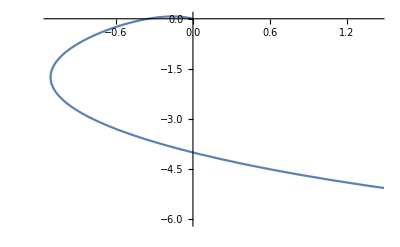

```mathematica
ListLinePlot[us]
```

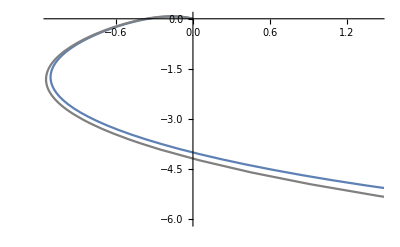

```mathematica
Show[ListLinePlot[us],ParametricPlot[Evaluate[{x[t],y[t]}/.rule],{t,0,1},PlotStyle->Gray]]
```

```mathematica
ToString/@{0,2}
```

{0,2}

```mathematica
Slider[Dynamic[a]]
x=.
```

```mathematica
l=Dynamic[a+1]
```

```mathematica
l
```

```mathematica
PadRight[{1,2,3},4]
```

{1,2,3,0}

```mathematica
RewriteInputFile=Export["C:\\Users\\Alex\\Documents\\Qt\\BMSTU\\NumMethods Semester 6\\NumMethods_Sem6_Lab_1\\input_test.txt",StringRiffle[ToString/@{#id,Length@#vars},"\n"]]&
```

Export[C:\Users\Alex\Documents\Qt\BMSTU\NumMethods Semester 6\NumMethods_Sem6_Lab_1\input_test.txt,StringRiffle[ToString/@{#id,Length[#vars]},
]]&

```mathematica
RewriteInputFile[systems[[1]]]
```

C:\Users\Alex\Documents\Qt\BMSTU\NumMethods Semester 6\NumMethods_Sem6_Lab_1\input_test.txt

### Расчет порядка

### Пример с x Sin[π/(2 x)]:

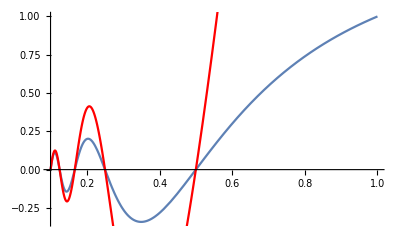

```mathematica
Show[Plot[x^1 Sin[π/(2 x)],{x,0.1,1}],ListLinePlot[tu,PlotStyle->Red]]
```

```mathematica
x Sin[π/(2 x)]/.x->0.1
```

6.12323×10^-17

```mathematica
D[x Sin[π/(2 x)],x]/.x->0.1
```

15.708

### Область устойчивости метода предиктор-корректор

```mathematica
(*μ=α+ⅈ β*)
μ=.
leftSide=(ⅇ^(4ⅈ ϕ)-(1+7/6 μ+55/64 μ^2)ⅇ^(3ⅈ ϕ)+(5/24 μ+59/64 μ^2)ⅇ^(2ⅈ ϕ)-(1/24 μ+37/64 μ^2)ⅇ^(ⅈ ϕ)+9/64 μ^2)
```

ⅇ^(4 ⅈ ϕ)+(9 μ^2)/64-ⅇ^(ⅈ ϕ) (μ/24+(37 μ^2)/64)-ⅇ^(3 ⅈ ϕ) (1+(7 μ)/6+(55 μ^2)/64)+ⅇ^(2 ⅈ ϕ) ((5 μ)/24+(59 μ^2)/64)

```mathematica
pcComplexBoundryPoints=Table[Module[{sol},
sol=NSolve[
leftSide==0,
{μ}
];
μ/.First@sol
]
,{ϕ,0,2 π,π/200}];
```

```mathematica
pcBoundryPoints=Table[Module[{sol},
sol=NSolve[
{
Cos[4 ϕ]==(1+7/6 α+55/64(α^2-β^2))Cos[3ϕ]-(7/6 β+55/32 α β)Sin[3ϕ]-(5/24 α+59/64(α^2-β^2))Cos[2 ϕ]+(5/24 β+59/32 α β)Sin[2 ϕ]+(1/24 α+37/64(α^2-β^2))Cos[ϕ]-(1/24 β+37/32 α β)Sin[ϕ]-9/64(α^2-β^2),
Sin[4 ϕ]==(1+7/6 α+55/64(α^2-β^2))Sin[3ϕ]+(7/6 β+55/32 α β)Cos[3ϕ]-(5/24 α+59/64(α^2-β^2))Sin[2 ϕ]-(5/24 β+59/32 α β)Cos[2 ϕ]+(1/24 α+37/64(α^2-β^2))Sin[ϕ]+(1/24 β+37/32 α β)Cos[ϕ]-9/32 α β
},
{α,β},Reals
];
{α,β}/.First@sol
]
,{ϕ,0,2 π,π/50}];
```

```mathematica
ListLinePlot[pcBoundryPoints]
```

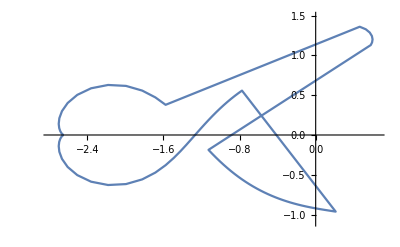

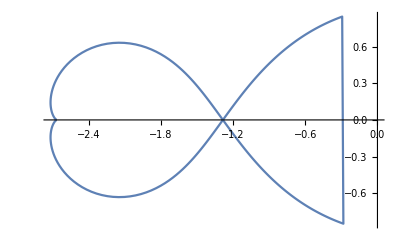

```mathematica
ComplexListPlot[pcComplexBoundryPoints,Joined->True]
```